## 0. Packages loading and nb definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
(* Canal completamente depolarizante que actúa sobre el primer espín de una cadena de N espines *)
DepolarizingChannel[ρ_,L_]:=
Module[{kraus},
(* Construir operadores de Kraus *)
kraus=KroneckerProduct[#,IdentityMatrix[2^(L-1)]]&/@ArrayReshape[IdentityMatrix[4]/√2,{4,2,2}];

(* Aplicar canal en su forma de Kraus a ρ *)
Total[#.ρ.ConjugateTranspose[#]&/@kraus]
]
```

```mathematica
(* Funciones para implementar cada uno de los términos de eq:appendix:A:2 *)
t1EqAppA2[t_,ψ0E_,eigenvalsH_,eigenvecsH_]:=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]/4

t2EqAppA2[t_,ψ0E_,eigenvalsH_,eigenvecsH_]:=-2*Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]/4

t3EqAppA2[t_,ψ0E_,eigenvalsH_,eigenvecsH_]:=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]/4
```

## 1. Analytic check

## 0.1 Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

```mathematica
superoperators=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2.csv"][[2;;]](*la primera fila tiene la info*)];
```

```mathematica
(* Check de que un superoperador random sea el correcto comparando con la construccion de alguno  *)
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *);
MatrixForm[Round[#,10.^-7]]&/@{Chop@Superoperator[t,ψ0E[[2]](*número de estado aleatorio*),eigenvalsH,eigenvecsH,L],superoperators[[t/0.1+1]]}
Equal@@%
```

{(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365),(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365)}

True

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Transpose[{Range[0,50,0.1],Chop[Purity/@chois]}];
```

### Buscando una matriz de Choi con 3 eigenvalores distintos de cero

En t=0.1 la matriz de Choi tiene 3 eigenvalores distintos de cero:

```mathematica
Chop[Eigenvalues/@chois][[1;;10]]
```

{{1.,0,0,0},{0.990571,0.00942882,7.1102×10^-10,0},{0.962127,0.0378731,1.611×10^-7,6.34061×10^-9},{0.917729,0.0822674,3.61008×10^-6,3.2418×10^-7},{0.864172,0.135792,0.0000311566,4.93318×10^-6},{0.810132,0.189672,0.000158488,0.0000378668},{0.76307,0.236173,0.000572634,0.000184883},{0.725874,0.271861,0.00161379,0.000650498},{0.695952,0.298531,0.00373108,0.00178679},{0.668433,0.320188,0.00732188,0.00405679}}

```mathematica
Select[Chop[Eigenvalues/@chois],Count[#,x_/;x==0]==1&]
```

{{0.990571,0.00942882,7.1102×10^-10,0}}

```mathematica
Table[{t,Chop@Eigenvalues[1/2Reshuffle[Superoperator[t,ψ0E[[1]],eigenvalsH,eigenvecsH,L]]]},{t,Power[10.,Range[-1,0,0.1]]}]
```

{{0.1,{0.990941,0.00905903,1.02617×10^-9,0}},{0.125893,{0.985525,0.0144751,6.35322×10^-9,0}},{0.158489,{0.976908,0.0230921,3.90888×10^-8,9.23572×10^-10}},{0.199526,{0.963309,0.0366906,2.38371×10^-7,9.07454×10^-9}},{0.251189,{0.942179,0.0578193,1.43501×10^-6,8.80243×10^-8}},{0.316228,{0.91027,0.0897205,8.4763×10^-6,8.35387×10^-7}},{0.398107,{0.864572,0.135371,0.0000486914,7.62972×10^-6}},{0.501187,{0.805695,0.193971,0.000269064,0.0000649}},{0.630957,{0.746266,0.251834,0.00142095,0.000479169}},{0.794328,{0.715535,0.274624,0.00716329,0.00267805}},{1.,{0.706809,0.252229,0.0310831,0.0098782}}}

```mathematica
TableForm[Chop@,TableHeadings->{None,{Style[TraditionalForm[HoldForm[t]],20],Text[Style["Choi eigenvalues",Black,20]]}},TableSpacing->{5,2}]
```

t | Choi eigenvalues
0.1 | 0.990941
0.00905903
1.02617×10^-9
0
0.125893 | 0.985525
0.0144751
6.35322×10^-9
0
0.158489 | 0.976908
0.0230921
3.90888×10^-8
9.23572×10^-10
0.199526 | 0.963309
0.0366906
2.38371×10^-7
9.07454×10^-9
0.251189 | 0.942179
0.0578193
1.43501×10^-6
8.80243×10^-8
0.316228 | 0.91027
0.0897205
8.4763×10^-6
8.35387×10^-7
0.398107 | 0.864572
0.135371
0.0000486914
7.62972×10^-6
0.501187 | 0.805695
0.193971
0.000269064
0.0000649
0.630957 | 0.746266
0.251834
0.00142095
0.000479169
0.794328 | 0.715535
0.274624
0.00716329
0.00267805
1. | 0.706809
0.252229
0.0310831
0.0098782

## 1. Analytic Choi matrix check

```mathematica
MatrixForm@Table[
{q,r}=IntegerDigits[i,2,2]+1;{p,s}=IntegerDigits[j,2,2]+1;
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{s-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{r-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]/2
,{i,0,3},{j,0,3}]
```

(0.246192+0. ⅈ | 0.0154966+0.00356999 ⅈ | -0.000178027-0.00466358 ⅈ | 0.00614217+0.00118478 ⅈ
0.0154966-0.00356999 ⅈ | 0.246958+0. ⅈ | 0.0100395+0.00520072 ⅈ | -0.022327-0.00607428 ⅈ
-0.000178027+0.00466358 ⅈ | 0.0100395-0.00520072 ⅈ | 0.253808+0. ⅈ | -0.0154966-0.00356999 ⅈ
0.00614217-0.00118478 ⅈ | -0.022327+0.00607428 ⅈ | -0.0154966+0.00356999 ⅈ | 0.253042+0. ⅈ)

```mathematica
MatrixForm[chois[[t/0.1+1]]]
```

(0.246192 | 0.0154966+0.00356999 ⅈ | -0.000178027-0.00466358 ⅈ | 0.00614217+0.00118478 ⅈ
0.0154966-0.00356999 ⅈ | 0.246958 | 0.0100395+0.00520072 ⅈ | -0.022327-0.00607428 ⅈ
-0.000178027+0.00466358 ⅈ | 0.0100395-0.00520072 ⅈ | 0.253808 | -0.0154966-0.00356999 ⅈ
0.00614217-0.00118478 ⅈ | -0.022327+0.00607428 ⅈ | -0.0154966+0.00356999 ⅈ | 0.253042)

## 2. Analytic Choi’s purity check

```mathematica
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *)
```

13.4

### eq:choi:chaometer:purity:1

```mathematica
(*  Calcular {pureza numérica, pureza analítica con eq:choi:chaometer:purity:1} *)
{Select[choiPurities,#[[1]]==t&],Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2},{q,2}]}
```

{{{13.4,0.252964}},0.252964}

### eq:choi:chaometer :purity:2 (Echo de Loschmidt)

```mathematica
(* Calcular la pureza analítica con eq:choi:chaometer:purity:2, echo de Loshcmidt *)
ψ1=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{#}],ψ0E[[2]]],eigenvalsH,eigenvecsH]&/@{0,1};
ρ1=Total[Dyad[#]&/@ψ1]/2;(* U (I/2 ⊗ ψψ) U^† *)
ρ2=DepolarizingChannel[ρ1,L];
Chop@Total[Braket[#,ρ2.#]&/@ψ1]
```

0.252964

### eq:appendix:A:1

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:1 *)
t1=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,p}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

1.00299

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:1 *)
t2=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

0.00958805

```mathematica
{Select[choiPurities,#[[1]]==t&],(t1+t2)/4}
```

{{{46.6,0.253144}},0.253144}

### eq:appendix:A:2

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:2 para confirmar que es igual a 2 *)
t1=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
```

2.

```mathematica
(* Calcular la suma de los primeros dos términos dentro del paréntesis de eq:appendix:A:2. Debería ser igual al primer término de eq:appendix:A:1 *)
t2=-2*Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]
```

-0.997548+0. ⅈ

```mathematica
(* Calcular el tercer término dentro del paréntesis de eq:appendix:A:2 *)
t3=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

0.00933467

```mathematica
(* Calcular la suma de todos los términos para revisar que sí de la pureza *)
{Select[choiPurities,#[[1]]==t&],(t1+t2+t3)/4}
```

{{{13.5,0.252947}},0.252947+0. ⅈ}

### eq:appendix:A:3

Es necesario revisar nada más el tercer término porque los primeros dos son iguales a los de la ecuación eq:appendix:A:2.

Sí son iguales los terceros términos de las ecuaciones eq:appendix:A:2 y eq:appendix:A:3

```mathematica
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *)
```

46.6

```mathematica
(* Calcular el tercer término de la ecuación eq:appendix:A:3 *)
1/2*Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
```

0.00239701

```mathematica
(* Calcular el tercer término de la ecuación eq:appendix:A:2 *)
t3EqAppA2[t,ψ0E[[2]],eigenvalsH,eigenvecsH]
```

0.00239701

## Purity worked more

```mathematica
(* primer término de la pureza analítica *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,p}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2}]
```

0.250966

```mathematica
(* primer término de la pureza analítica *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].IdentityMatrix[2^L].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
]^2/4
,{i,2},{j,2}]
```

0.5

```mathematica
t=1.2
```

1.2

```mathematica
(* segundo término de la pureza analítica *)
-Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]/2
```

-0.219887+0. ⅈ

```mathematica
0.5+%37
```

0.250603+0. ⅈ

```mathematica
Times@@Chop[(superoperators[[0.6/0.1+1]].{1/2,0,0,1/2})[[{1,4}]]]
```

0.249998

## Choi’s purity of a Hamiltonian from GOE

```mathematica
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
t=0.01;
```

```mathematica
(*pureza matriz de Choi*)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2},{q,2}]
```

0.861003

```mathematica
(*segundo término pureza matriz de Choi *)
-Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]/2
```

-0.249623+0. ⅈ

```mathematica
(*tercer término pureza matriz de Choi *)
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2}]
```

0.000355922

```mathematica
0.5+%90+%91
```

0.250287+0. ⅈ

## Pureza con Hamiltoniano GOE

```mathematica
L=10;
```

```mathematica
(* Calcular un Hamiltoniano de GOE y obtener sus eigenvalores y eigenvectores *)
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
(*U=MatrixExp[-I H];*)
{eigenvalsH,eigenvecsH}=Chop[Eigensystem[H]];
]
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
t2=Table[t2EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

```mathematica
(*tercer término pureza matriz de Choi *)
t3=Table[t3EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

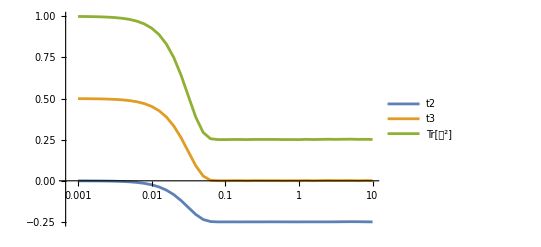

```mathematica
ListLogLinearPlot[Transpose[{Power[10.,Range[-3,1,0.1]],#}]&/@{t2/4,t3/4,(2+t2+t3)/4},
Joined->True,
PlotLegends->{"t2","t3",TraditionalForm[HoldForm[Tr[𝒟^2]]]}
]
```

## Pureza con Hamiltoniano con P(s) Poissoniana

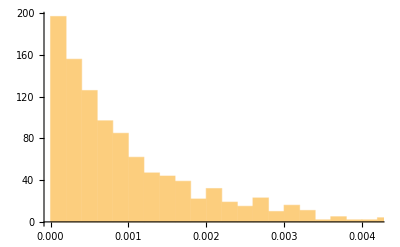

```mathematica
(*Set the size of the matrix*)
n=2^L;

(*Create a diagonal matrix with uniformly distributed random entries*)
d=DiagonalMatrix[RandomReal[{0,1},n]];

(*Optionally,apply a random unitary transformation*)
A=RandomComplex[{-1,1},{n,n}]; (*Generate a random complex matrix*)
{U,R}=QRDecomposition[A];
RandomMatrix=Transpose[U].d.U;

(*Get the eigenvalues*)
eigenvalues=Eigenvalues[RandomMatrix];

(*Plot the level spacing distribution*)
Histogram[Differences[Sort[Chop@eigenvalues]]]
```

```mathematica
(*Set the size of the matrix*)
n=2^L;

(*Create a diagonal matrix with uniformly distributed random entries*)
eigenvalsH=RandomReal[{0,1},n];

(*Optionally,apply a random unitary transformation*)
A=RandomComplex[{-1,1},{n,n}]; (*Generate a random complex matrix*)
{U,R}=QRDecomposition[A];
eigenvecsH=Transpose[U];
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
t2=Table[t2EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

```mathematica
(*tercer término pureza matriz de Choi *)
t3=Table[t3EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

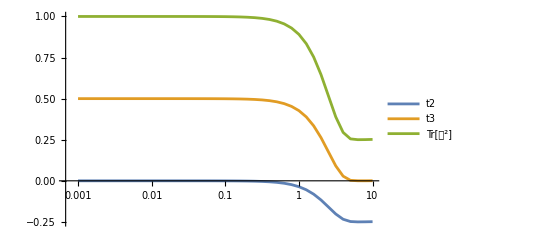

```mathematica
ListLogLinearPlot[Transpose[{Power[10.,Range[-3,1,0.1]],#}]&/@{t2/4,t3/4,(2+t2+t3)/4},
Joined->True,
PlotLegends->{"t2","t3",TraditionalForm[HoldForm[Tr[𝒟^2]]]}
]
```

## Pureza en region regular

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
t2=Table[t2EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

```mathematica
(*tercer término pureza matriz de Choi *)
t3=Table[t3EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

```mathematica
(* Ticks personalizados para las gráficas en escala log *)
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
```

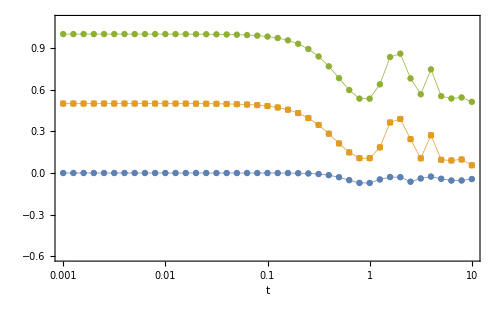

```mathematica
ListLogLinearPlot[Transpose[{Power[10.,Range[-3,1,0.1]],#}]&/@{t2/4,t3/4,(2+t2+t3)/4},
PlotRange->{{10^(-3),10},{-0.6,1.1}},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Table[y,{y,-0.5,1,0.25}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:1 *)
t=0;
Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2},{q,2}]
```

1.